# QHD for a general potential

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

Quantized Hamilton Dynamics (QHD) is applied to the a general potential. QHD gives an approximation to the Heisenberg Equations of Motion (EOM). The QHD commands used in this document are included in QUANTUM, which is a free Mathematica add-on that can be downloaded from
 http://homepage.cem.itesm.mx/lgomez/quantum/
This tutorial shows how to use the QUANTUM Mathematica add-on to reproduce the results and graphs from Prezhdo and Pereverzev in J. Chem. Phys., Vol 116, No. 11, March 2002, pages 4450-4461
 http://homepage.cem.itesm.mx/lgomez/quantum/QHDgeneralpotential.pdf .

## Load the Package

First load the Quantum`QHD` package. Write:
Needs["Quantum`QHD`"]
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package and print a welcome message:

```mathematica
Needs["Quantum`QHD`"]
```

Quantum`QHD` 
A Mathematica package for Quantized Hamilton Dynamics approximation to Heisenberg Equations of Motion
by José Luis Gómez-Muñoz
based on the original idea of Kirill Igumenshchev

This add-on does NOT work properly with the debugger turned on. Therefore the debugger must NOT be checked in the Evaluation menu of Mathematica.

Execute SetQHDAliases[] in order to use the keyboard to enter QHD objects
SetQHDAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetQHDAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. Remember that SetQuantumAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetQHDAliases[]
```

ALIASES:
[ESC]on[ESC]     · Quantum concatenation symbol
[ESC]time[ESC]   𝓉 Time symbol
[ESC]hb[ESC]     ℏ Reduced Planck's constant (h bar)
[ESC]ii[ESC]     ⅈ Imaginary I symbol
[ESC]inf[ESC]    ∞ Infinity symbol
[ESC]->[ESC]     → Option (Rule) symbol
[ESC]ave[ESC]    ⟨□⟩ Quantum average template
[ESC]expec[ESC]  ⟨□⟩ Quantum average template
[ESC]symm[ESC]   (□·□)_𝓈 Symmetrized quantum product template
[ESC]comm[ESC]   ⟦□,□⟧_- Commutator template
[ESC]po[ESC]     (□)^□ Power template
[ESC]su[ESC]     □_□ Subscripted variable template
[ESC]posu[ESC]   □_□^□ Power of a subscripted variable template
[ESC]fra[ESC]    □/□ Fraction template
[ESC]eva[ESC]    □/.{□→□,□→□} Evaluation (ReplaceAll) template

SetQHDAliases[] must be executed again in each new notebook that is created, only one time per notebook.

## Commutation Relationship

Here we define the commutation relationship that will be used in this document.
In order to enter the templates and symbols ⟦□,□⟧_-, ℏ and ⅈ you can either use the QHD palette (toolbar) or press the keys [ESC]comm[ESC], [ESC]hb[ESC] and [ESC]ii[ESC]

```mathematica
Clear[q,p];
SetQuantumObject[q,p];
⟦q,p⟧_-=ⅈ*ℏ
```

ⅈ ℏ

## Moving Frame Approximation to the Potential Energy

The potential energy is expanded in Taylor series around the instantaneous average value of the position variable ⟨q⟩. This is the “moving frame approximation”. Please remember that the command SetQuantumObject was used above in order to define q as a quantum operator. The fourth order moving frame approximation to the potential energy is stored in the variable v4 below:

```mathematica
v4=∑_(j=0)^4 D[ v[⟨q⟩],{⟨q⟩,j} ]/(j!)(q-⟨q⟩)^j
```

v[⟨q⟩]+(q-⟨q⟩) v'[⟨q⟩]+1/2 (q-⟨q⟩)^2 v''[⟨q⟩]+1/6 (q-⟨q⟩)^3 v^(3)[⟨q⟩]+1/24 (q-⟨q⟩)^4 v^(4)[⟨q⟩]

Using a unitary mass, the Hamiltonian is stored in h4 below:

```mathematica
h4=p^2/2+v4
```

p^2/2+v[⟨q⟩]+(q-⟨q⟩) v'[⟨q⟩]+1/2 (q-⟨q⟩)^2 v''[⟨q⟩]+1/6 (q-⟨q⟩)^3 v^(3)[⟨q⟩]+1/24 (q-⟨q⟩)^4 v^(4)[⟨q⟩]

## Second-Order QHD with a Fourth-Order Moving-Frame Expansion of the Potential

The evolution of the average of an observable A in the Heisenberg representation is given by the equation of motion (EOM): 
 ⅈ ℏ d/dt⟨A⟩=⟨[A,H]⟩
Consider the averages of momentum, position and their products ⟨p⟩, ⟨q⟩, ⟨p^2⟩, ⟨q^2⟩, ⟨pq⟩, ⟨p^3⟩, ⟨p^2 q⟩... The EOMs for the average values are coupled and, in general, form an infinite hierarchy of equations. Quantized Hamilton Dynamics (QHD) terminates this hierarchy by the approximation of the higher order averages via products of the lower order averages. For instance the approximation
⟨ABC⟩≈⟨AB⟩⟨C⟩+⟨AC⟩⟨B⟩+⟨BC⟩⟨A⟩-2⟨A⟩⟨B⟩⟨C⟩
can be used to approximate the third-order averages ⟨q^3⟩ and ⟨pq^2⟩_𝓈 in terms of the first and second order averages ⟨p⟩, ⟨q⟩, ⟨p^2⟩, ⟨q^2⟩ and ⟨p·q⟩_s=⟨(p·q+q·p)/2⟩. 
The command QHDHierarchy (see below) takes as its first argument the QHD order, the second argument is the variable which is used to start the hierarchy, and the third argument is the Hamiltonian. The resulting hierarchy is stored in the variable hier4 and it is shown in a nice format using the command QHDForm below:

```mathematica
hier4=QHDHierarchy[2,q,h4];
QHDForm[hier4,QHDLabel->"Compare with Prezhdo and Pereverzev \nJ.Chem.Phys. Vol 116 No 11, March 2002\nPages 4450-4461 Eqs.(15)-(19)"]
```

Compare with Prezhdo and Pereverzev 
J.Chem.Phys. Vol 116 No 11, March 2002
Pages 4450-4461 Eqs.(15)-(19)
(d⟨q⟩)/d𝓉=⟨p⟩
(d⟨p⟩)/d𝓉=-v'(⟨q⟩)+1/2 ⟨q⟩^2 v^(3)(⟨q⟩)-1/2 ⟨q^2⟩ v^(3)(⟨q⟩)
(d⟨q^2⟩)/d𝓉=2 ⟨pq⟩_𝓈
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩-⟨q⟩ v'(⟨q⟩)+⟨q⟩^2 v''(⟨q⟩)-⟨q^2⟩ v''(⟨q⟩)+1/2 ⟨q⟩^3 v^(3)(⟨q⟩)-1/2 ⟨q⟩ ⟨q^2⟩ v^(3)(⟨q⟩)-1/2 ⟨q⟩^4 v^(4)(⟨q⟩)+⟨q⟩^2 ⟨q^2⟩ v^(4)(⟨q⟩)-1/2 ⟨q^2⟩^2 v^(4)(⟨q⟩)
(d⟨p^2⟩)/d𝓉=-2 ⟨p⟩ v'(⟨q⟩)+2 ⟨p⟩ ⟨q⟩ v''(⟨q⟩)-2 ⟨pq⟩_𝓈 v''(⟨q⟩)+⟨p⟩ ⟨q⟩^2 v^(3)(⟨q⟩)-⟨p⟩ ⟨q^2⟩ v^(3)(⟨q⟩)-⟨p⟩ ⟨q⟩^3 v^(4)(⟨q⟩)+⟨p⟩ ⟨q⟩ ⟨q^2⟩ v^(4)(⟨q⟩)+⟨q⟩^2 ⟨pq⟩_𝓈 v^(4)(⟨q⟩)-⟨q^2⟩ ⟨pq⟩_𝓈 v^(4)(⟨q⟩)

## Example: Double Well with a Third-Order Moving-Frame Expansion of the Potential

The potential energy that will be used in this example is
V=-5 q^2+q^4
It is used by Prezhdo and Pereverzev in their paper  J. Chem. Phys., Vol 116, No. 11, March 2002, pages 4450-4461
 http://homepage.cem.itesm.mx/lgomez/quantum/QHDgeneralpotential.pdf, this is a “double well”potential energy, see the graph below:

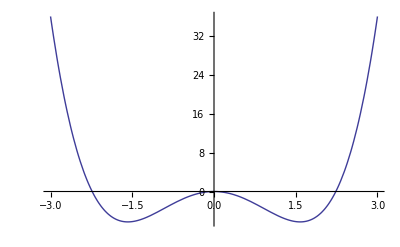

```mathematica
Plot[-5 q^2+q^4,{q,-3,3}]
```

This is a third-order moving frame approximation to the potential, see below:

```mathematica
Clear[a,b];
vd[q_]:=a*q^2+b*q^4;
vd3=∑_(j=0)^3 D[ vd[⟨q⟩],{⟨q⟩,j} ]/(j!)(q-⟨q⟩)^j
```

4 b (q-⟨q⟩)^3 ⟨q⟩+a ⟨q⟩^2+b ⟨q⟩^4+1/2 (q-⟨q⟩)^2 (2 a+12 b ⟨q⟩^2)+(q-⟨q⟩) (2 a ⟨q⟩+4 b ⟨q⟩^3)

Using a unitary mass, the Hamiltonian is stored in hd3 below:

```mathematica
hd3=p^2/2+vd3
```

p^2/2+4 b (q-⟨q⟩)^3 ⟨q⟩+a ⟨q⟩^2+b ⟨q⟩^4+1/2 (q-⟨q⟩)^2 (2 a+12 b ⟨q⟩^2)+(q-⟨q⟩) (2 a ⟨q⟩+4 b ⟨q⟩^3)

The commands below calculate and show the second order QHD hierarchy of equations for the third order moving frame approximation to the double-well. The command QHDHierarchy takes as its first argument the QHD order, the second argument is the variable which is used to start the hierarchy, and the third argument is the Hamiltonian. The resulting hierarchy is stored in the variable hierd3 and it is shown in a nice format using the command QHDForm below:

```mathematica
hierd3=QHDHierarchy[2,q,hd3];
QHDForm[hierd3]
```

Closure procedure was applied to order 2
(d⟨q⟩)/d𝓉=⟨p⟩
(d⟨p⟩)/d𝓉=-2 a ⟨q⟩+8 b ⟨q⟩^3-12 b ⟨q⟩ ⟨q^2⟩
(d⟨q^2⟩)/d𝓉=2 ⟨pq⟩_𝓈
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩+20 b ⟨q⟩^4-2 a ⟨q^2⟩-24 b ⟨q⟩^2 ⟨q^2⟩
(d⟨p^2⟩)/d𝓉=40 b ⟨p⟩ ⟨q⟩^3-24 b ⟨p⟩ ⟨q⟩ ⟨q^2⟩-4 a ⟨pq⟩_𝓈-24 b ⟨q⟩^2 ⟨pq⟩_𝓈

A QHD hierarchy can be shown in a graph using the command QHDGraphPlot on the output of QHDHierachy. Arrows point from a first dynamical variable to a second dynamical variable that includes the first one in its EOM; please compare the table above with the graph below:

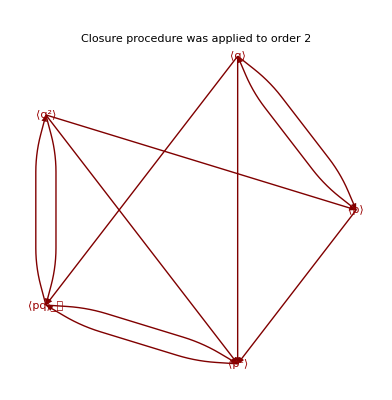

```mathematica
QHDGraphPlot[hierd3]
```

Next we evaluate the hierarchy when the parameter a takes the value of -5 and b takes the value of 1, and the result of that evaluation is stored in the variable numhierd3:

```mathematica
numhierd3= hierd3/. {a->-5,b->1};
QHDForm[ numhierd3 ]
```

Closure procedure was applied to order 2
(d⟨q⟩)/d𝓉=⟨p⟩
(d⟨p⟩)/d𝓉=10 ⟨q⟩+8 ⟨q⟩^3-12 ⟨q⟩ ⟨q^2⟩
(d⟨q^2⟩)/d𝓉=2 ⟨pq⟩_𝓈
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩+20 ⟨q⟩^4+10 ⟨q^2⟩-24 ⟨q⟩^2 ⟨q^2⟩
(d⟨p^2⟩)/d𝓉=40 ⟨p⟩ ⟨q⟩^3-24 ⟨p⟩ ⟨q⟩ ⟨q^2⟩+20 ⟨pq⟩_𝓈-24 ⟨q⟩^2 ⟨pq⟩_𝓈

The command QHDInitialConditionsTemplate generates an initial conditions template for the hierarchy:

```mathematica
QHDInitialConditionsTemplate[numhierd3 , 0]
```

{⟨q⟩[0]==■,⟨p⟩[0]==■,⟨q^2⟩[0]==■,⟨(p·q)_𝓈⟩[0]==■,⟨p^2⟩[0]==■}

Copy-paste the output of the previous command as input in the next one. Fill in the placeholders (■) with the appropiate initial values. Those initial values can be numbers. On the other hand, in the calculation below they are symbols like po, and then these symbols are evaluated at the desired numerical values. The initial conditions are stored in the variable inicond3 below:

```mathematica
inicond3={⟨q⟩[0]==qo,⟨p⟩[0]==po,⟨q^2⟩[0]==qo^2+ℏ/(2ω),⟨Subscript[(p·q), 𝓈]⟩[0]==po*qo,⟨p^2⟩[0]==po^2+(ℏ*ω)/2}/.{ℏ->1,po->0,qo-> -√(5/2),ω->√(-4a)}/.{a->-5}
```

{⟨q⟩[0]==-√(5/2),⟨p⟩[0]==0,⟨q^2⟩[0]==5/2+1/(4 √5),⟨(p·q)_𝓈⟩[0]==0,⟨p^2⟩[0]==√5}

The command QHDNDSolve takes as arguments the numerical version of the hierarchy (which was stored in the variable numhierd3), the initial conditions (which were stored in inicond3), the initial time and the final time. The output of this command is the numerical solution of the differential equations, in the form of InterpolatingFunction objects. This output can be used to plot (graph) the dynamical variables as functions of time, as it will be shown below in this document. The output is stored in the variable sold3 in the calculation below:

```mathematica
sold3=QHDNDSolve[numhierd3,inicond3,0,3]
```

{{⟨q⟩→InterpolatingFunction[{{0.,3.}},<>],⟨p⟩→InterpolatingFunction[{{0.,3.}},<>],⟨q^2⟩→InterpolatingFunction[{{0.,3.}},<>],⟨(p·q)_𝓈⟩→InterpolatingFunction[{{0.,3.}},<>],⟨p^2⟩→InterpolatingFunction[{{0.,3.}},<>]}}

The command command QHDPlot takes as its second argument the output of QHDNDSolve, which was stored in the variable sold3. The first argument specifies the dynamical variables or expression that we want to plot (graph) as a function of time. If we want to plot all the dynamical variables, the first argument must be the word All, see the five plots below:

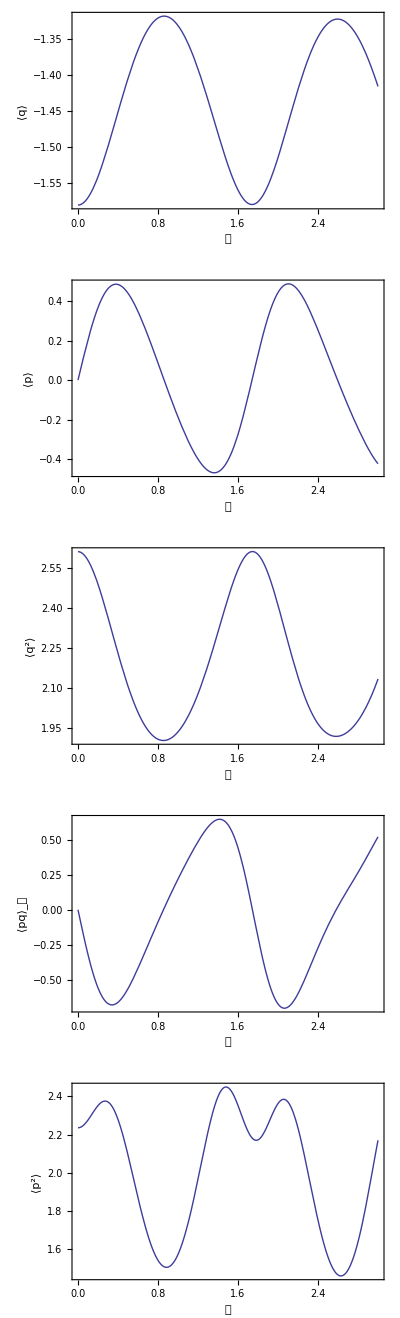

```mathematica
QHDPlot[All,sold3]
```

Next command generates the plot of ⟨q⟩ as a function of time. It reproduces part of a figure of the paper by Prezhdo and Pereverzev, see the graph below:

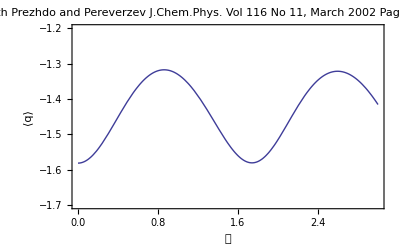

```mathematica
QHDPlot[q,sold3,
PlotRange->{-1.7,-1.2},
AxesOrigin->{0,-√(5/2)},Axes->True,
PlotLabel->"Compare with Prezhdo and Pereverzev \nJ.Chem.Phys. Vol 116 No 11, March 2002\nPages 4450-4461 Fig. 2(a)"
]
```

A different set of initial conditions is stored in inicond3b below:

```mathematica
inicond3b={⟨q⟩[0]==qo,⟨p⟩[0]==po,⟨q^2⟩[0]==qo^2+ℏ/(2ω),⟨Subscript[(p·q), 𝓈]⟩[0]==po*qo,⟨p^2⟩[0]==po^2+(ℏ*ω)/2}/.{ℏ->1,po->0,qo-> -22/10,ω->√(-4a)}/.{a->-5}
```

{⟨q⟩[0]==-11/5,⟨p⟩[0]==0,⟨q^2⟩[0]==121/25+1/(4 √5),⟨(p·q)_𝓈⟩[0]==0,⟨p^2⟩[0]==√5}

Solution of the differential equations with the new initial conditions:

```mathematica
sold3b=QHDNDSolve[numhierd3,inicond3b,0,1.5]
```

{{⟨q⟩→InterpolatingFunction[{{0.,1.5}},<>],⟨p⟩→InterpolatingFunction[{{0.,1.5}},<>],⟨q^2⟩→InterpolatingFunction[{{0.,1.5}},<>],⟨(p·q)_𝓈⟩→InterpolatingFunction[{{0.,1.5}},<>],⟨p^2⟩→InterpolatingFunction[{{0.,1.5}},<>]}}

Next command generates the plot of ⟨q⟩ as a function of time. It reproduces part of a figure of the paper by Prezhdo and Pereverzev, it shows a particle initially localize in the left minimum on the potential, and in the long run becoming equally split between the two wells, see the graph below:

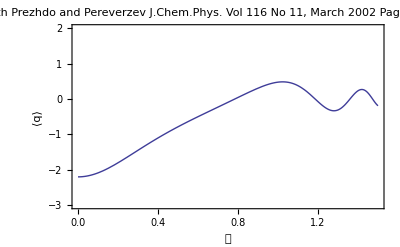

```mathematica
QHDPlot[q,sold3b,
PlotRange->{-3,2},
AxesOrigin->{0,0},Axes->True,
PlotLabel->"Compare with Prezhdo and Pereverzev \nJ.Chem.Phys. Vol 116 No 11, March 2002\nPages 4450-4461 Fig. 2(b)"
]
```

This tutorial shows how to use the QUANTUM Mathematica add-on to reproduce the results and graphs from Prezhdo and Pereverzev in J. Chem. Phys., Vol 116, No. 11, March 2002, pages 4450-4461
 http://homepage.cem.itesm.mx/lgomez/quantum/QHDgeneralpotential.pdf .

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx